```mathematica
<<ASTRAINterpret`
```

```mathematica
SetDirectory["C:\\Users\\jkj62\\Documents\\GitHub\\OnlineModel\\SimulationFramework\\Examples\\CLARA\\Ultrashort\\MOGA\\"]
```

C:\Users\jkj62\Documents\GitHub\OnlineModel\SimulationFramework\Examples\CLARA\Ultrashort\MOGA

```mathematica
iterationdir="iteration_5\\";
```

## Twiss Analysis

```mathematica
ASTRAemitInterpret[iterationdir<>#<>".Zemit.001"&/@Select[{"injector400","S02","L02","S03","L03","S04","L4H","S05","VBC","S06","L04","S07"},FileExistsQ[iterationdir<>#<>".Zemit.001"]&],ASTRAVerbose->False]
```

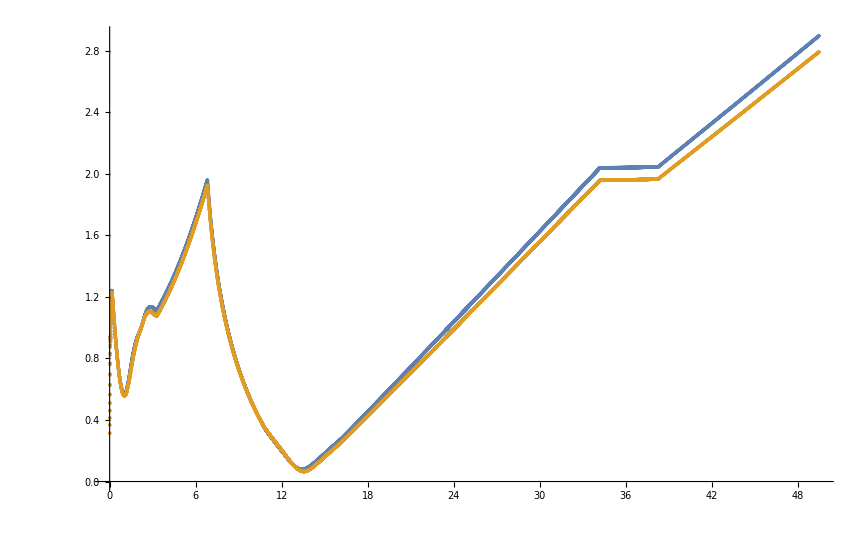

```mathematica
ListPlot[{Transpose[{z[[1;;Length[xrms]]],xrms}],Transpose[{z[[1;;Length[yrms]]],yrms}]},PlotRange->{All,{0,All}}]
```

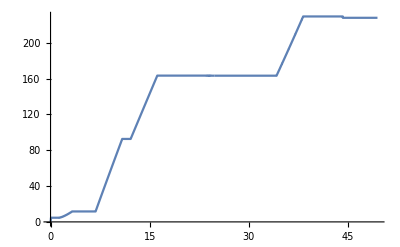

```mathematica
ListLinePlot[{Transpose[{z,Ekin}]},PlotRange->All]
```

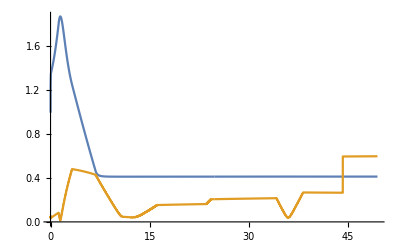

```mathematica
ListLinePlot[{Transpose[{z,10^12(zrms/(1000*3 10^8))}],Transpose[{z,ΔErms/1000}]},PlotRange->All]
```

## Beam Analysis

```mathematica
ASTRABeamInterpret[iterationdir<>"S07.4948.001",ASTRAVerbose->False]
```

Columns Redefined: x [m], y [m], z [m], px [eV/c], py [eV/c], pz [eV/c], clock [ns], charge [nC], index [DimensionlessUnit], status [DimensionlessUnit]

```mathematica
t=(z-Mean[z])/QuantityMagnitude[UnitConvert[Quantity["SpeedOfLight"]]];
```

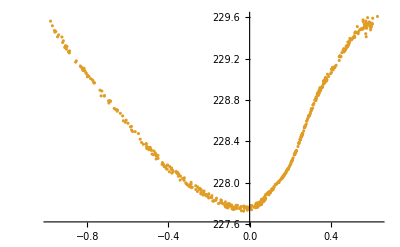

```mathematica
ListPlot[{#[[{1}]],#}&[Transpose[{10^12(t-Mean[t]),pz/10^6}]]]
```

```mathematica
slicelength=10^12(Max[t]-Min[t])/10;
$CHARGE=250;
```

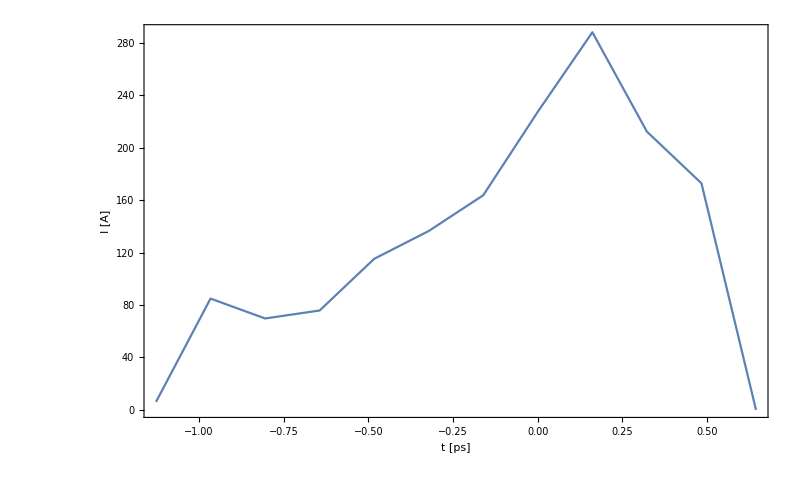

```mathematica
ListLinePlot[{#[[1]],Append[#[[2]],0]}//Transpose,elsplotstyle,Frame->True,PlotRange->All,FrameLabel->{"t [ps]","I [A]"}]&[{1,250/(slicelength Length[t])}HistogramList[#,{slicelength}]&[10^12(t-Mean[t])]]
```

```mathematica
tn=10^12(t-Mean[t]);
```

```mathematica
FWHM[data_,frac_:2]:=Block[{x,y,max},
{x,y}=Transpose[data];
If[frac<1,
max=Max[y]*frac,
max=Max[y]/frac];
tf=Transpose[{x,Map[#>max&,y]}];
{Position[tf,True][[{1,-1},1]],
Differences[Select[tf,#[[2]]==True&][[{1,-1}]]][[1,1]]}
]
```

```mathematica
SKcurrentDist=SmoothKernelDistribution[tn];
```

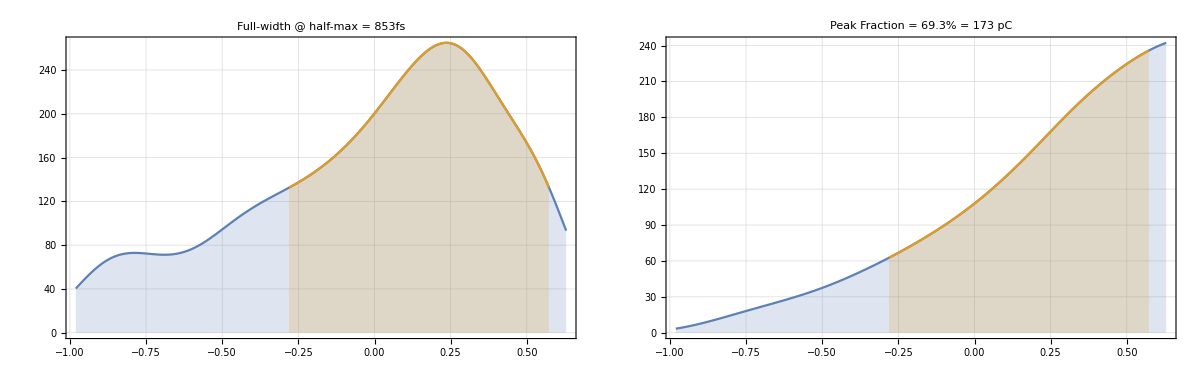

0.161958

```mathematica
bw=RootMeanSquare[tn]/2^8;
{fwhmpos,fwhm}=FWHM[Table[{x,PDF[SKcurrentDist,x]},{x,Min[tn],Max[tn],bw}],2];
{fwqmpos,fwqm}=FWHM[Table[{x,PDF[SKcurrentDist,x]},{x,Min[tn],Max[tn],bw}],2];
pdfdata=Table[{x, PDF[SKcurrentDist,x]},{x,Min[tn],Max[tn],bw}];
cdfdata=Table[{x,100 CDF[SKcurrentDist,x]},{x,Min[tn],Max[tn],bw}];
GraphicsRow[{ListLinePlot[{{1,250}#&/@pdfdata,{1,250}#&/@Take[pdfdata,fwhmpos]},Filling->Bottom,PlotRange->All,PlotLabel->"Full-width @ half-max = "<>ToString[Round[10^3 fwhm,1]]<>"fs",PlotTheme->"Detailed"],ListLinePlot[{{1,250/100}#&/@cdfdata,{1,250/100}#&/@Take[cdfdata,fwhmpos]},Filling->Bottom,PlotRange->All,PlotLabel->"Peak Fraction = "<>ToString[Round[Differences[Take[cdfdata,fwhmpos][[{1,-1},2]]][[1]],0.1]]<>"% = "<>ToString[Round[250/100 Differences[Take[cdfdata,fwhmpos][[{1,-1},2]]][[1]],1]]<>" pC",PlotTheme->"Detailed"]},ImageSize->1200,Spacings->0]
StandardDeviation[Take[pdfdata,fwhmpos][[All,2]]]/Max[pdfdata[[All,2]]]
(*Export["C:\\Users\\jkj62\\Pictures\\FEBE\\5kA\\FWHM.png",%,ImageResolution->200]*)
```